# Bosonic Complexity of Purification (BCoP)

IMPORTANT: Please read the instructions/advice carefully before running the file.

```mathematica
Quit[];
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

First step: Import the GaussianOptimization Package (Run):

```mathematica
Import["/Users/HugoCamargo89/Desktop/gaussian_purifications/Mathematica Code/GaussianOptimization.m"]
```

```mathematica
(*<<GaussianOptimization`*)
```

In this Mathematica notebook we use the optimization procedure to find the complexity of purification for two bosonic systems. The first system, studied in the first Chapter is a lattice free scalar field theory with periodic conditions. This Chapter is called Bosons on a Periodic Lattice.
 
The second system, studied in the second Chapter, as a free scalar field theory undergoing a smooth quench through a critical point. This Chapter is called Bosons under a Smooth Quench Through a Critical Point.

## Chapter 1: Bosons on a Periodic Lattice

In this Chapter of the Mathematica notebook, we use the optimization procedure to find the complexity of purification CoP for a bosonic system on a periodic lattice. The SubChapter: Definitions, should be run at the beginning, as it has the necessary field-theoretic definitions for the physical system in question.

This part of the notebook is divided into  four scenarios. Each one of these is also divided into several sections, each one with a number of subsections. These are organized as follows:

1. In Scenario 1 we look at bosonic complexity of purification BCoP, as a function of lattice separation d between subsystems with fixed total number of sites N for a scalar field mass of m=1/10 with variable subsystem sizes dim1 and dim2.

2. In Scenario 2 we look at BCoP, as a function of subsystem size dim1 dim2 with fixed d=0 lattice separation between subsystems for a scalar field mass of m=1/10 with variable N.

3. In Scenario 3 we look at BCoP, as a function of subsystem size dim1 dim2 with variable lattice separation d between subsystems for a scalar field mass of m=1/10 with variable N.

4. In Scenario 4 we look at BCoP, as a function of total number of lattice sites N with fixed subsystem size dim1 dim2 for a scalar field mass of m=1/10 with variable subsystem separation d.

In each Scenario, there are several Cases that are studied individually, where the rest of the parameters is varied. Each Case is divided into Subcases. At the end of each Case, a Summary for the Case contains the relevant outcome of the numerical optimization for the given Case. Atfter all the cases have been studied for a given Scenario, a Summary for the Scenario is presented, with the relevant information for the setup.

IMPORTANT: Scenario 1 is currently being studied. Scenarios 2, 3, 4 are pending.

Definitions (Run)

The following definitions are equivalent to the ones used in Michal and Lucas’ recent work on complexity for the thermofield double theory. The parameters of the theory are the following:

1. Total number of lattice sites: N,
2. Mass of the Scalar Field: m,
3. Lattice Spacing: l,
4. Dimension of subsystems on the lattice: dim1 & dim2,
5. Lattice Site Separation between the subsystems: d,
6. Total length of the circle: L==(N-1)l .

The relevant quantities that are calculated from these parameters are the full covariance matrix of the vacuum state of the theory (assuming a small mass m) CM[N,m,l], as well as the partial covariance matrix for the subsystem consisting of two sets of lattice sites. These can be set to be adjacent or disjoint, depending on the parameter d (lattice site separation between the subsystems) partialCM[N,m,l,d,dim1,dim2].

```mathematica
FourierMatrixElement[N_]:=Function[{k,x},Exp[I 2 Pi x k /N]/Sqrt[N]];
DispersionRelation[m_,N_,l_]:=Function[{k},Sqrt[m^2+4/l^2  (Sin[Pi k/N])^2]];
```

```mathematica
FT[n_]:=Module[{f,pos,val},
f=FourierMatrixElement[n];
pos=Table[{x,k},{k,n},{x,n}]//Flatten[#,1]&;
val=Table[f[k,x]//N,{k,n},{x,n}]//Flatten[#,1]&;
SparseArray[pos->val]];
```

```mathematica
Diag[m_,n_,l_]:=Module[{ω},
ω=DispersionRelation[m,n,l];
DiagonalMatrix[Table[ω[k],{k,n}]]];
```

```mathematica
invDiag[m_,n_,l_]:=Module[{ω},
ω=DispersionRelation[m,n,l];
DiagonalMatrix[Table[1/ω[k],{k,n}]]];
```

```mathematica
CM[N_,m_,l_]:=Module[{F,D,invD,G,Tr},
F=FT[N];D=Diag[m,N,l]; invD=invDiag[m,N,l];
G=ArrayFlatten[({{F.D.ConjugateTranspose[F], 0}, {0, F.invD.ConjugateTranspose[F]}})]//Chop//SparseArray];
```

```mathematica
partialCM[N_,m_,l_,d_,dim1_,dim2_]:=
Module[{dim, halfdim, bigCM, indices1, indices2,indices, partialCM, Tr},

bigCM=CM[N,m,l];
dim=Length[bigCM]; halfdim=dim/2;

indices1=Thread[{Table[x,{x,dim1}],Table[x+halfdim,{x,dim1}]}]//Flatten[#,1]&;
indices2=Thread[{Table[dim1+d+x,{x,dim2}],Table[dim1+d+x+halfdim,{x,dim2}]}]//Flatten[#,1]&;

indices=Join[indices1,indices2];

partialCM=bigCM[[indices,indices]]];
```

Scenario 1: BCoP as a Function of Subsystem Partition Separation (Fixed Bipartite Subsystem Size) with m=1/10:

In this Scenario, we look at bosonic complexity of purification BCoP, as a function of lattice separation d between subsystems with fixed total number of sites N for a scalar field mass of m=1/10 with variable subsystem sizes dim1 and dim2. This scenario is interesting, as it will tell us about the behaviour of complexity of purification in the case where the subsystem in a mixed state is comprised of two regions in the lattice. By varying the separation between the regions that make up the subsystem, we can study the effect that separating the subregions has on the complexity of the purified state.

This Scenario consists of 5 Cases. The difference between the Cases studied is the total length L of the periodic lattice.

1. Case 1: N=100, m=1/10, δ=1 ;  ( N-1)δ == L=99

2. Case 2: N=100, m=1/10, δ=1/10;  (N-1)δ == L=9.9

3. Case 3: N=10, m=1/10, δ=1 ;  (N-1)δ == L=9

4. Case 4: N=10, m=1/10, δ=1/10 ; (N-1)δ == L=0.9

5. Case 5: N=300, m=1/10, δ=1 ; (N-1)δ == L=299

Each Case is followed by Subcases, where the dimension of the subsystem regions dim1 = dim2 is varied. For Each Subcase,  BCoP is calculated for a given subsystem region separation d. At the end of the Section, a graph is shown which presents the results of the optimization for BCoP as a function of subsystem separation: BCoP[d].

IMPORTANT: At the moment of writing this sentence (04.09.19 - 13:21), only Case 1 is being studied. Cases 2,3,4,5 are pending.

UPDATE (04.09.19 - 13:21): SubCases 1.1. , 1.2 , and 1.3 where studied a previous version of the Optimization Algorithm, which does not take into account the newest specifications (according to the .m file from 30.08.19). SubCase 1.4 is being studied with the most recent function definitions (version 04.09.19 by Lucas).

UPDATE (04.09.19 - 13:21): Results for SubCases 1.1, 1.2, and 1.3 can be found in a subsection within each section called Summary.

UPDATE (06.09.19 - 16:30): Simplified the analysis of results using the revised version of the Optimization package (version 06.09.19 by Lucas).

UPDATE (09.09.19 - 11:50): Optimized SubCase Analysis. SubCases 1.1. , 1.2 , and 1.3 are studied again with the newest Optimization Package.

UPDATE (10.09.19 - 11:30): Added an extra subcase to test symmetry in BCoP (Spolier alert: doesn’t seem to be symmetric under the exchange of partitions).

## Case 1: N=100, m=1/10, δ=1 ; (N-1)δ == L=99

### SubCase 1.1: N=100, m=1/10, δ=1, dimA1=dimB1=1

```mathematica
sites=100;
mass=1/10;
latticespacing=1;
dimA1=1;
dimB1=1;
dimPur=dimA1+dimB1;
Arrayseplist={{0},{1},{2},{3},{4},{5},{8},{10},{12},{15},{20},{30},{45},{46},{47},{48},{49}};
seplist=Flatten[Arrayseplist];
```

```mathematica
TableCM0=Table[partialCM[100,mass,latticespacing,seplist[[i]],dimA1,dimB1],{i,1,Length[seplist]}];
```

```mathematica
Table[Table[GOExtractStdFormG[TableCM0[[i]]],{i,1,Length[TableCM0]}][[j]],{j,1,Length[seplist]}];
```

```mathematica
rlist=Table[Table[GOExtractStdFormG[TableCM0[[i]]],{i,1,Length[TableCM0]}][[j]],{j,1,Length[seplist]}][[All,1]];
MTra=Table[Table[GOExtractStdFormG[TableCM0[[i]]],{i,1,Length[TableCM0]}][[j]],{j,1,Length[seplist]}][[All,2]];
```

```mathematica
JT=Table[GOPurifyStandardJBoson[rlist[[i]],dimPur,"qpqp"],{i,Length[seplist]}];
JR0=GOTransformGtoJ[IdentityMatrix[2(dimA1+dimB1+dimPur)],"qpqp","qpqp"];
```

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra[[i]]],0},{0,IdentityMatrix[2dimPur]}}]//SparseArray,{i,Length[seplist]}];
```

```mathematica
function=Table[GOCoPBos[JT[[i]]],{i,Length[seplist]}]; 
gradient=Table[GOCoPgradBos[JT[[i]]],{i,Length[seplist]}];
```

```mathematica
ProblemSpecific=Table[{function[[i]],gradient[[i]]},{i,Length[seplist]}];
```

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSpNoUN[dimPur]}];
metric=GOMetricSp[LieBasis,JR0];
newM[m_,s_,x_]:=GOapproxExp[s,x].m;
```

```mathematica
SystemSpecific=Table[{JR0,{M0List[[i]]},LieBasis,IdentityMatrix[Length[LieBasis]],newM},{i,Length[M0List]}];
```

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-10; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

```mathematica
(*{Time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];*)
```

```mathematica
Timing[GOOptimize[ProblemSpecific[[1]],SystemSpecific[[1]],ProcedureSpecific]]
```

{0.707561}

Reason for termination: Function value tolerance reached

{0.059735,{{0.707459},{SparseArray[…]},{3,3,3,3},{{0.707561,0.70746,0.707459,0.707459,0.707459}},{{0.707561,0.70746,0.707459,0.707459,0.707459}},{{0.198185,0.0121276,0.000751171,0.0000480823,3.33129×10^-6}}}}

```mathematica
Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,2]][[All,1]]
```

{{0.707459},{0.767223},{0.780635},{0.787262},{0.79114},{0.793601},{0.797171},{0.798164},{0.798703},{0.799105},{0.799346},{0.799434},{0.799442},{0.799442},{0.799442},{0.799443},{0.799443}}

```mathematica
ListSubCase11=Join[Arrayseplist,Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,2]][[All,1]],2];
```

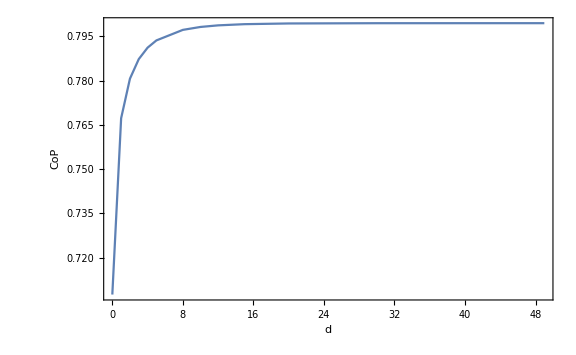

```mathematica
ListPlot[ListSubCase11,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

In this case, Complexity of Purification (CoP) seems to be monotonically increasing with the distance between the subsystems. There is no plateau-like structure for small separation. It can also be seen that for a separation of order 10^1, CoP saturates.

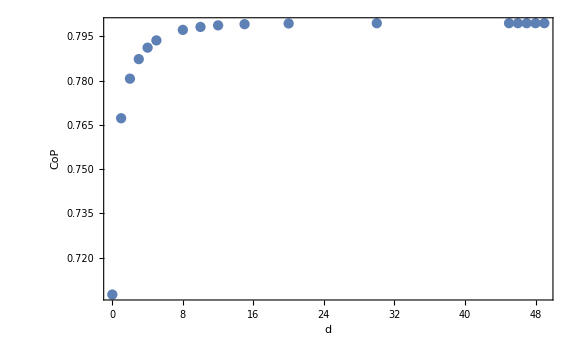
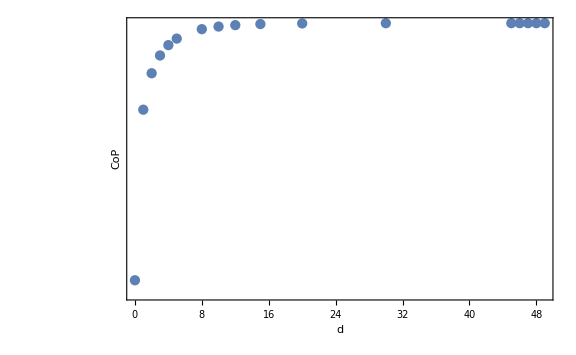

```mathematica
PlotListSubCase11=Row[{ListPlot[ListSubCase11,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50],ListLogPlot[ListSubCase11,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]}]
Export[NotebookDirectory[]<>"PlotListSubCase11.pdf",PlotListSubCase11];
```

```mathematica
Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,1]]
```

{0.055985,0.072577,0.067841,0.068742,0.069764,0.05509,0.059346,0.058956,0.05997,0.058424,0.059124,0.060084,0.062249,0.061462,0.072243,0.063182,0.071024}

```mathematica
(*Time=Table[Timing[GOOptimize[{function[[i]],gradient[[i]]},{JR0,M0List[[i]],LieBasis,IdentityMatrix[Length[LieBasis]],newM},ProcedureSpecific]][[All,1]],{i,Length[seplist]}]*)
```

```mathematica
(*Result=Table[Timing[GOOptimize[{function[[i]],gradient[[i]]},{JR0,M0List[[i]],LieBasis,IdentityMatrix[Length[LieBasis]],newM},ProcedureSpecific]][[All,2]],{i,Length[seplist]}];*)
```

```mathematica
(*Print["Time taken: ",Time," seconds"];
Print["Final value: ",Table[(Result[[i]])⟦1,1⟧,{i,Length[seplist]}]];
Print["Number of iterations: ",Length[Result⟦4,1⟧]];
Print["Number of total corrections: ",Result⟦3⟧//Total];
ListPlot[Result⟦4⟧, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]*)
(* We plot all items in the finalElist object in the result to ensure a correct plot in the case of multiple results *)
```

### SubCase 1.2: N=100, m=1/10, δ=1, dimA1=dimB1=2

```mathematica
sites=100;
mass=1/10;
latticespacing=1;
dimA1=2;
dimB1=2;
dimPur=dimA1+dimB1;
Arrayseplist={{0},{1},{2},{3},{4},{5},{8},{10},{15},{20},{30},{40},{43},{47},{48}};
seplist=Flatten[Arrayseplist];
```

```mathematica
TableCM0=Table[partialCM[sites,mass,latticespacing,seplist[[i]],dimA1,dimB1],{i,1,Length[seplist]}];
```

```mathematica
Table[Table[GOExtractStdFormG[TableCM0[[i]]],{i,1,Length[TableCM0]}][[j]],{j,1,Length[seplist]}];
```

```mathematica
rlist=Table[Table[GOExtractStdFormG[TableCM0[[i]]],{i,1,Length[TableCM0]}][[j]],{j,1,Length[seplist]}][[All,1]];
MTra=Table[Table[GOExtractStdFormG[TableCM0[[i]]],{i,1,Length[TableCM0]}][[j]],{j,1,Length[seplist]}][[All,2]];
```

```mathematica
JT=Table[GOPurifyStandardJBoson[rlist[[i]],dimPur,"qpqp"],{i,Length[seplist]}];
JR0=GOTransformGtoJ[IdentityMatrix[2(dimA1+dimB1+dimPur)],"qpqp","qpqp"];
```

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra[[i]]],0},{0,IdentityMatrix[2dimPur]}}]//SparseArray,{i,Length[seplist]}];
```

```mathematica
function=Table[GOCoPBos[JT[[i]]],{i,Length[seplist]}]; 
gradient=Table[GOCoPgradBos[JT[[i]]],{i,Length[seplist]}];
```

```mathematica
ProblemSpecific=Table[{function[[i]],gradient[[i]]},{i,Length[seplist]}];
```

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSpNoUN[dimPur]}];
metric=GOMetricSp[LieBasis,JR0];
newM[m_,s_,x_]:=GOapproxExp[s,x].m;
```

```mathematica
SystemSpecific=Table[{JR0,{M0List[[i]]},LieBasis,IdentityMatrix[Length[LieBasis]],newM},{i,Length[M0List]}];
```

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-10; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

```mathematica
(*{Time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];*)
```

```mathematica
Timing[GOOptimize[ProblemSpecific[[1]],SystemSpecific[[1]],ProcedureSpecific]]
```

{0.890909}

Reason for termination: Function value tolerance reached

{0.217086,{{0.890738},{SparseArray[…]},{3,3,3,3},{{0.890909,0.890738,0.890738,0.890738,0.890738}},{{0.890909,0.890738,0.890738,0.890738,0.890738}},{{0.28892,0.0193999,0.00131881,0.0000915685,6.62964×10^-6}}}}

```mathematica
Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,2]][[All,1]]
```

{{0.890738},{0.956594},{0.973802},{0.982673},{0.987995},{0.991432},{0.996523},{0.99797},{0.999362},{0.999723},{0.999857},{0.999869},{0.99987},{0.99987},{0.99987}}

```mathematica
ListSubCase12=Join[Arrayseplist,Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,2]][[All,1]],2];
```

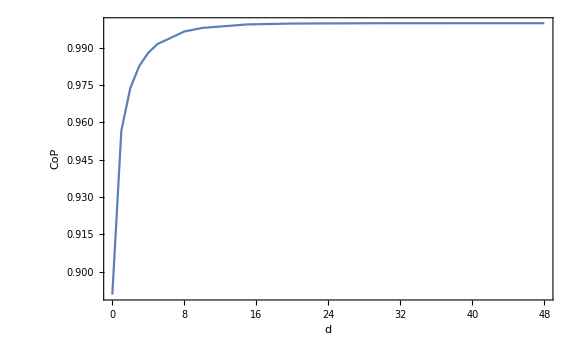

```mathematica
ListPlot[ListSubCase12,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

Also in this case, Complexity of Purification (CoP) seems to be monotonically increasing with the distance between the subsystems. There is no plateau-like structure for small separation. It can also be seen that for a separation of order 10^1, CoP saturates.

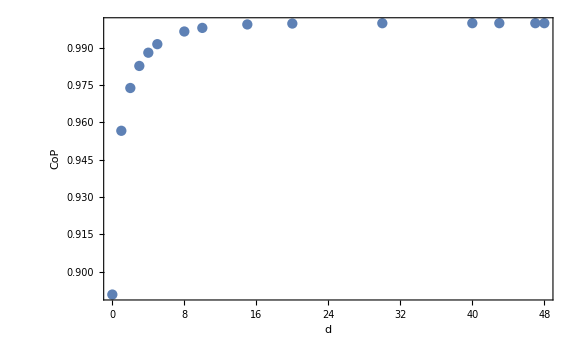
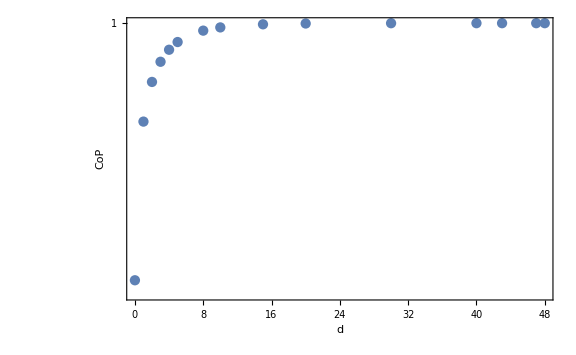

```mathematica
PlotListSubCase12=Row[{ListPlot[ListSubCase12,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50],ListLogPlot[ListSubCase12,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]}]
Export[NotebookDirectory[]<>"PlotListSubCase12.pdf",PlotListSubCase12];
```

```mathematica
Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,1]]
```

{0.227844,0.282007,0.255336,0.286777,0.294668,0.284054,0.269099,0.26952,0.263292,0.272644,0.29366,0.312723,0.258463,0.280649,0.274584}

### SubCase 1.3: N=100, m=1/10, δ=1, dimA1=dimB1=3

```mathematica
sites=100;
mass=1/10;
latticespacing=1;
dimA1=3;
dimB1=3;
dimPur=dimA1+dimB1;
Arrayseplist={{0},{1},{2},{3},{4},{5},{8},{10},{12},{15},{20},{30},{40},{45},{47}};
seplist=Flatten[Arrayseplist];
```

```mathematica
TableCM0=Table[partialCM[sites,mass,latticespacing,seplist[[i]],dimA1,dimB1],{i,1,Length[seplist]}];
```

```mathematica
Table[Table[GOExtractStdFormG[TableCM0[[i]]],{i,1,Length[TableCM0]}][[j]],{j,1,Length[seplist]}];
```

```mathematica
rlist=Table[Table[GOExtractStdFormG[TableCM0[[i]]],{i,1,Length[TableCM0]}][[j]],{j,1,Length[seplist]}][[All,1]];
MTra=Table[Table[GOExtractStdFormG[TableCM0[[i]]],{i,1,Length[TableCM0]}][[j]],{j,1,Length[seplist]}][[All,2]];
```

```mathematica
JT=Table[GOPurifyStandardJBoson[rlist[[i]],dimPur,"qpqp"],{i,Length[seplist]}];
JR0=GOTransformGtoJ[IdentityMatrix[2(dimA1+dimB1+dimPur)],"qpqp","qpqp"];
```

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra[[i]]],0},{0,IdentityMatrix[2dimPur]}}]//SparseArray,{i,Length[seplist]}];
```

```mathematica
function=Table[GOCoPBos[JT[[i]]],{i,Length[seplist]}]; 
gradient=Table[GOCoPgradBos[JT[[i]]],{i,Length[seplist]}];
```

```mathematica
ProblemSpecific=Table[{function[[i]],gradient[[i]]},{i,Length[seplist]}];
```

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSpNoUN[dimPur]}];
metric=GOMetricSp[LieBasis,JR0];
newM[m_,s_,x_]:=GOapproxExp[s,x].m;
```

```mathematica
SystemSpecific=Table[{JR0,{M0List[[i]]},LieBasis,IdentityMatrix[Length[LieBasis]],newM},{i,Length[M0List]}];
```

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-10; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

```mathematica
(*{Time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];*)
```

```mathematica
Timing[GOOptimize[ProblemSpecific[[1]],SystemSpecific[[1]],ProcedureSpecific]]
```

{1.03559}

Reason for termination: Function value tolerance reached

{0.652715,{{1.0354},{SparseArray[…]},{3,3,3,3},{{1.03559,1.0354,1.0354,1.0354,1.0354}},{{1.03559,1.0354,1.0354,1.0354,1.0354}},{{0.32725,0.0225747,0.0015711,0.00011032,7.86735×10^-6}}}}

```mathematica
Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,2]][[All,1]]
```

{{1.0354},{1.09587},{1.11317},{1.12242},{1.12812},{1.13188},{1.13761},{1.13931},{1.14026},{1.14101},{1.1415},{1.14171},{1.14174},{1.14175},{1.14175}}

```mathematica
ListSubCase13=Join[Arrayseplist,Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,2]][[All,1]],2];
```

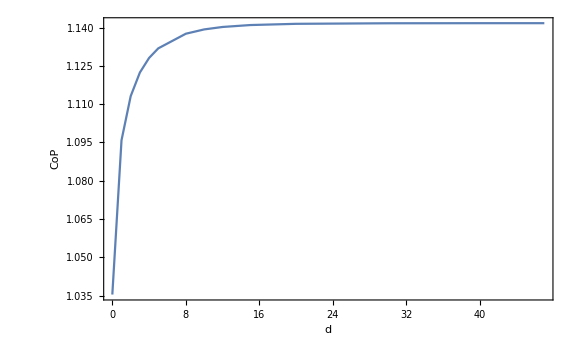

```mathematica
ListPlot[ListSubCase13,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

Also in this case, Complexity of Purification (CoP) seems to be monotonically increasing with the distance between the subsystems. There is no plateau-like structure for small separation. It can also be seen that for a separation of order 10^1, CoP saturates.

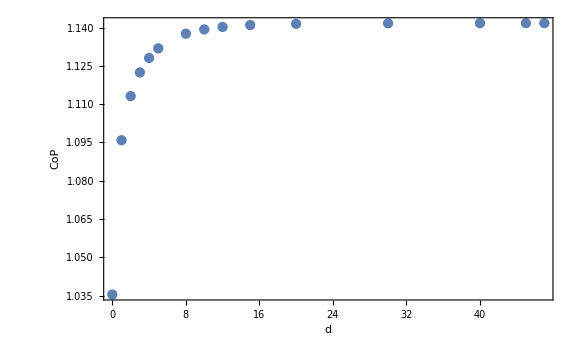
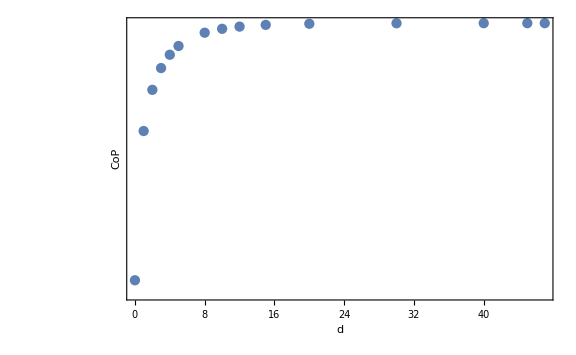

```mathematica
PlotListSubCase13=Row[{ListPlot[ListSubCase13,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50],ListLogPlot[ListSubCase13,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]}]
Export[NotebookDirectory[]<>"PlotListSubCase13.pdf",PlotListSubCase13];
```

```mathematica
Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,1]]
```

{1.2439,0.966847,0.900752,0.962163,0.981216,0.992001,0.870228,0.884011,0.862918,0.987563,0.829316,0.823881,0.793269,0.812787,0.839079}

### Extra SubCase: N=100, m=1/10, δ=1, Different partition dimensions (Small subsystem size)

#### a) dimA1=1, dimB1=3

```mathematica
sites=100;
mass=1/10;
latticespacing=1;
dimA1=1;
dimB1=3;
dimPur=dimA1+dimB1;
Arrayseplist={{0},{1},{2},{3},{4},{5},{8},{10},{12},{15},{20},{30},{40},{45},{47},{48}};
seplist=Flatten[Arrayseplist];
```

```mathematica
TableCM0=Table[partialCM[sites,mass,latticespacing,seplist[[i]],dimA1,dimB1],{i,1,Length[seplist]}];
```

```mathematica
Table[Table[GOExtractStdFormG[TableCM0[[i]]],{i,1,Length[TableCM0]}][[j]],{j,1,Length[seplist]}];
```

```mathematica
rlist=Table[Table[GOExtractStdFormG[TableCM0[[i]]],{i,1,Length[TableCM0]}][[j]],{j,1,Length[seplist]}][[All,1]];
MTra=Table[Table[GOExtractStdFormG[TableCM0[[i]]],{i,1,Length[TableCM0]}][[j]],{j,1,Length[seplist]}][[All,2]];
```

```mathematica
JT=Table[GOPurifyStandardJBoson[rlist[[i]],dimPur,"qpqp"],{i,Length[seplist]}];
JR0=GOTransformGtoJ[IdentityMatrix[2(dimA1+dimB1+dimPur)],"qpqp","qpqp"];
```

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra[[i]]],0},{0,IdentityMatrix[2dimPur]}}]//SparseArray,{i,Length[seplist]}];
```

```mathematica
function=Table[GOCoPBos[JT[[i]]],{i,Length[seplist]}]; 
gradient=Table[GOCoPgradBos[JT[[i]]],{i,Length[seplist]}];
```

```mathematica
ProblemSpecific=Table[{function[[i]],gradient[[i]]},{i,Length[seplist]}];
```

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSpNoUN[dimPur]}];
metric=GOMetricSp[LieBasis,JR0];
newM[m_,s_,x_]:=GOapproxExp[s,x].m;
```

```mathematica
SystemSpecific=Table[{JR0,{M0List[[i]]},LieBasis,IdentityMatrix[Length[LieBasis]],newM},{i,Length[M0List]}];
```

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-10; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

```mathematica
(*{Time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];*)
```

```mathematica
Timing[GOOptimize[ProblemSpecific[[1]],SystemSpecific[[1]],ProcedureSpecific]]
```

{0.890909}

Reason for termination: Function value tolerance reached

{0.348258,{{0.890738},{SparseArray[…]},{3,3,3,3},{{0.890909,0.890738,0.890738,0.890738,0.890738}},{{0.890909,0.890738,0.890738,0.890738,0.890738}},{{0.28892,0.0193999,0.00131881,0.0000915685,6.62964×10^-6}}}}

```mathematica
Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,2]][[All,1]]
```

{{0.890738},{0.946472},{0.961211},{0.968975},{0.973707},{0.976809},{0.981528},{0.982928},{0.983728},{0.984365},{0.984789},{0.984974},{0.984994},{0.984995},{0.984995},{0.984995}}

```mathematica
ListSubCaseExtra1a=Join[Arrayseplist,Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,2]][[All,1]],2];
```

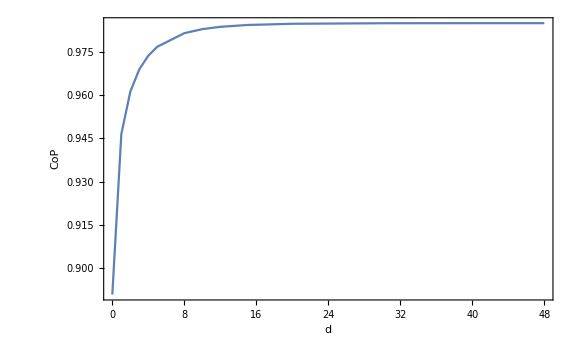

```mathematica
ListPlot[ListSubCaseExtra1a,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

Also in this case, Complexity of Purification (CoP) seems to be monotonically increasing with the distance between the subsystems. There is no plateau-like structure for small separation. It can also be seen that for a separation of order 10^1, CoP saturates.

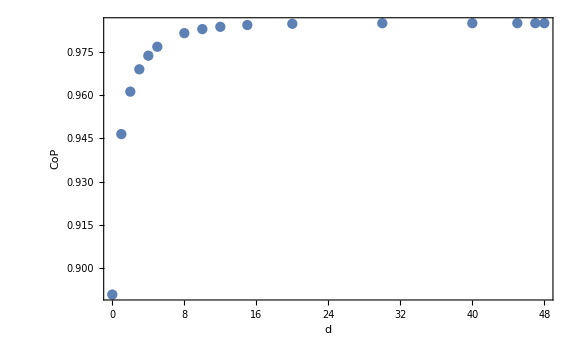
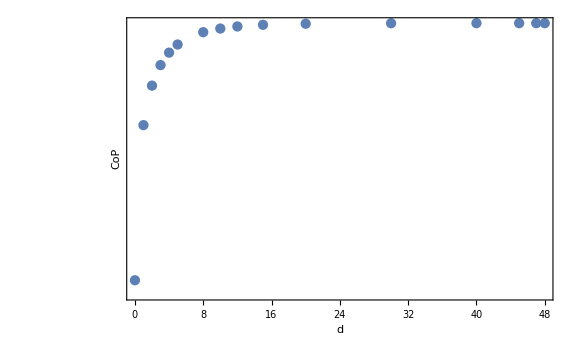

```mathematica
PlotListSubCaseExtra1a=Row[{ListPlot[ListSubCaseExtra1a,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50],ListLogPlot[ListSubCaseExtra1a,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]}]
Export[NotebookDirectory[]<>"PlotListSubCaseExtra1a.pdf",PlotListSubCaseExtra1a];
```

```mathematica
Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,1]]
```

{0.403361,0.485164,0.446,0.475024,0.487448,0.479368,0.463134,0.451076,0.446952,0.490727,0.45736,0.456635,0.447038,0.454477,0.409885,0.393586}

#### b) dimA1=3, dimB1=1

```mathematica
sites=100;
mass=1/10;
latticespacing=1;
dimA1=3;
dimB1=1;
dimPur=dimA1+dimB1;
Arrayseplist={{0},{1},{2},{3},{4},{5},{8},{10},{12},{15},{20},{30},{40},{45},{47},{48}};
seplist=Flatten[Arrayseplist];
```

```mathematica
TableCM0=Table[partialCM[sites,mass,latticespacing,seplist[[i]],dimA1,dimB1],{i,1,Length[seplist]}];
```

```mathematica
Table[Table[GOExtractStdFormG[TableCM0[[i]]],{i,1,Length[TableCM0]}][[j]],{j,1,Length[seplist]}];
```

```mathematica
rlist=Table[Table[GOExtractStdFormG[TableCM0[[i]]],{i,1,Length[TableCM0]}][[j]],{j,1,Length[seplist]}][[All,1]];
MTra=Table[Table[GOExtractStdFormG[TableCM0[[i]]],{i,1,Length[TableCM0]}][[j]],{j,1,Length[seplist]}][[All,2]];
```

```mathematica
JT=Table[GOPurifyStandardJBoson[rlist[[i]],dimPur,"qpqp"],{i,Length[seplist]}];
JR0=GOTransformGtoJ[IdentityMatrix[2(dimA1+dimB1+dimPur)],"qpqp","qpqp"];
```

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra[[i]]],0},{0,IdentityMatrix[2dimPur]}}]//SparseArray,{i,Length[seplist]}];
```

```mathematica
function=Table[GOCoPBos[JT[[i]]],{i,Length[seplist]}]; 
gradient=Table[GOCoPgradBos[JT[[i]]],{i,Length[seplist]}];
```

```mathematica
ProblemSpecific=Table[{function[[i]],gradient[[i]]},{i,Length[seplist]}];
```

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSpNoUN[dimPur]}];
metric=GOMetricSp[LieBasis,JR0];
newM[m_,s_,x_]:=GOapproxExp[s,x].m;
```

```mathematica
SystemSpecific=Table[{JR0,{M0List[[i]]},LieBasis,IdentityMatrix[Length[LieBasis]],newM},{i,Length[M0List]}];
```

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-10; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

```mathematica
(*{Time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];*)
```

```mathematica
Timing[GOOptimize[ProblemSpecific[[1]],SystemSpecific[[1]],ProcedureSpecific]]
```

{0.890909}

Reason for termination: Function value tolerance reached

{0.398633,{{0.890738},{SparseArray[…]},{3,3,3,3},{{0.890909,0.890738,0.890738,0.890738,0.890738}},{{0.890909,0.890738,0.890738,0.890738,0.890738}},{{0.28892,0.0193999,0.00131881,0.0000915685,6.62964×10^-6}}}}

```mathematica
Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,2]][[All,1]]
```

{{0.890738},{0.950635},{0.965851},{0.973723},{0.978483},{0.981584},{0.986252},{0.987614},{0.988381},{0.988981},{0.989368},{0.989529},{0.989545},{0.989547},{0.989547},{0.989547}}

```mathematica
ListSubCaseExtra1b=Join[Arrayseplist,Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,2]][[All,1]],2];
```

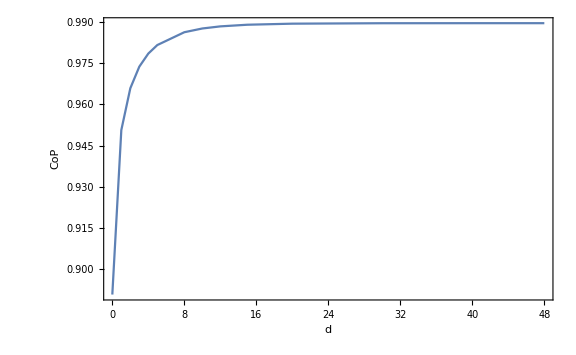

```mathematica
ListPlot[ListSubCaseExtra1b,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

Also in this case, Complexity of Purification (CoP) seems to be monotonically increasing with the distance between the subsystems. There is no plateau-like structure for small separation. It can also be seen that for a separation of order 10^1, CoP saturates.

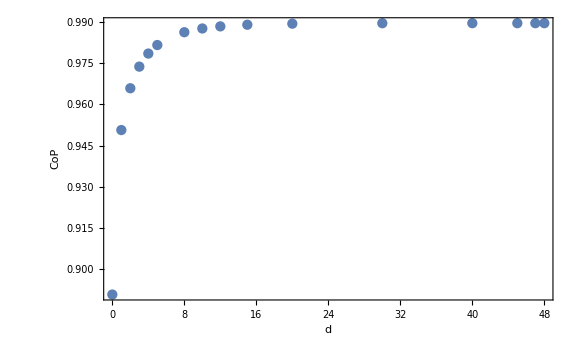
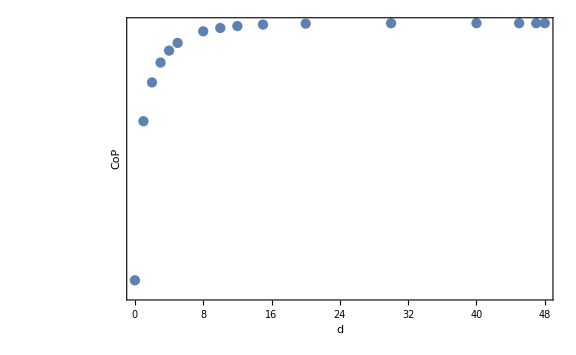

```mathematica
PlotListSubCaseExtra1b=Row[{ListPlot[ListSubCaseExtra1b,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50],ListLogPlot[ListSubCaseExtra1b,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]}]
Export[NotebookDirectory[]<>"PlotListSubCaseExtra1b.pdf",PlotListSubCaseExtra1b];
```

```mathematica
Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,1]]
```

{0.401627,0.62916,0.639944,0.606891,0.553317,0.654698,0.601997,0.589691,0.546838,0.627778,0.610417,0.613179,0.59877,0.508403,0.530557,0.549059}

#### c) Comparison

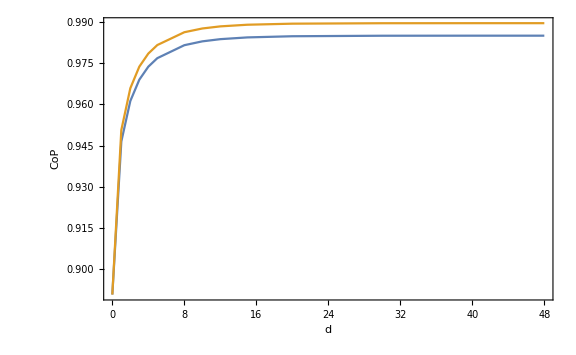

```mathematica
ListPlot[{ListSubCaseExtra1a,ListSubCaseExtra1b},PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

Aha! There seems to be a difference between the saturation values! So it is not completely symmetric! BCoP is sensitive to the exchange between subsystem partitions!

### Extra SubCase N=100, m=1/10, δ=1, dimA1=dimB1=1, Going all the way with separation (?)

```mathematica
sites=100;
mass=1/10;
latticespacing=1;
dimA1=1;
dimB1=1;
dimPur=dimA1+dimB1;
Arrayseplist={{0},{1},{2},{3},{4},{5},{8},{10},{12},{15},{20},{30},{45},{46},{47},{48},{49},{50},{51},{52},{53},{60},{70},{80},{85},{88},{90},{92},{93},{94},{95},{96},{97},{98}};
seplist=Flatten[Arrayseplist];
```

```mathematica
TableCM0=Table[partialCM[100,mass,latticespacing,seplist[[i]],dimA1,dimB1],{i,1,Length[seplist]}];
```

```mathematica
Table[Table[GOExtractStdFormG[TableCM0[[i]]],{i,1,Length[TableCM0]}][[j]],{j,1,Length[seplist]}];
```

```mathematica
rlist=Table[Table[GOExtractStdFormG[TableCM0[[i]]],{i,1,Length[TableCM0]}][[j]],{j,1,Length[seplist]}][[All,1]];
MTra=Table[Table[GOExtractStdFormG[TableCM0[[i]]],{i,1,Length[TableCM0]}][[j]],{j,1,Length[seplist]}][[All,2]];
```

```mathematica
JT=Table[GOPurifyStandardJBoson[rlist[[i]],dimPur,"qpqp"],{i,Length[seplist]}];
JR0=GOTransformGtoJ[IdentityMatrix[2(dimA1+dimB1+dimPur)],"qpqp","qpqp"];
```

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra[[i]]],0},{0,IdentityMatrix[2dimPur]}}]//SparseArray,{i,Length[seplist]}];
```

```mathematica
function=Table[GOCoPBos[JT[[i]]],{i,Length[seplist]}]; 
gradient=Table[GOCoPgradBos[JT[[i]]],{i,Length[seplist]}];
```

```mathematica
ProblemSpecific=Table[{function[[i]],gradient[[i]]},{i,Length[seplist]}];
```

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSpNoUN[dimPur]}];
metric=GOMetricSp[LieBasis,JR0];
newM[m_,s_,x_]:=GOapproxExp[s,x].m;
```

```mathematica
SystemSpecific=Table[{JR0,{M0List[[i]]},LieBasis,IdentityMatrix[Length[LieBasis]],newM},{i,Length[M0List]}];
```

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-10; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

```mathematica
(*{Time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];*)
```

```mathematica
Timing[GOOptimize[ProblemSpecific[[1]],SystemSpecific[[1]],ProcedureSpecific]]
```

{0.707561}

Reason for termination: Function value tolerance reached

{0.201458,{{0.707459},{SparseArray[…]},{3,3,3,3},{{0.707561,0.70746,0.707459,0.707459,0.707459}},{{0.707561,0.70746,0.707459,0.707459,0.707459}},{{0.198185,0.0121276,0.000751171,0.0000480823,3.33129×10^-6}}}}

```mathematica
Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,2]][[All,1]]
```

{0.707561}

Reason for termination: Function value tolerance reached

{0.767284}

Reason for termination: Function value tolerance reached

{0.780687}

Reason for termination: Function value tolerance reached

{0.787304}

Reason for termination: Function value tolerance reached

{0.791172}

Reason for termination: Function value tolerance reached

{0.793626}

Reason for termination: Function value tolerance reached

{0.797184}

Reason for termination: Function value tolerance reached

{0.798174}

Reason for termination: Function value tolerance reached

{0.798711}

Reason for termination: Function value tolerance reached

{0.799112}

Reason for termination: Function value tolerance reached

{0.799351}

Reason for termination: Function value tolerance reached

{0.799439}

Reason for termination: Function value tolerance reached

{0.799448}

Reason for termination: Function value tolerance reached

{0.799448}

Reason for termination: Function value tolerance reached

{0.799448}

Reason for termination: Function value tolerance reached

{0.799448}

Reason for termination: Function value tolerance reached

{0.799448}

Reason for termination: Function value tolerance reached

{0.799448}

Reason for termination: Function value tolerance reached

{0.799448}

Reason for termination: Function value tolerance reached

{0.799448}

Reason for termination: Function value tolerance reached

{0.799448}

Reason for termination: Function value tolerance reached

{0.799447}

Reason for termination: Function value tolerance reached

{0.799434}

Reason for termination: Function value tolerance reached

{0.79929}

Reason for termination: Function value tolerance reached

{0.798883}

Reason for termination: Function value tolerance reached

{0.798174}

Reason for termination: Function value tolerance reached

{0.797184}

Reason for termination: Function value tolerance reached

{0.795262}

Reason for termination: Function value tolerance reached

{0.793626}

Reason for termination: Function value tolerance reached

{0.791172}

Reason for termination: Function value tolerance reached

{0.787304}

Reason for termination: Function value tolerance reached

{0.780687}

Reason for termination: Function value tolerance reached

{0.767284}

Reason for termination: Function value tolerance reached

{0.707561}

Reason for termination: Function value tolerance reached

{{0.707459},{0.767223},{0.780635},{0.787262},{0.79114},{0.793601},{0.797171},{0.798164},{0.798703},{0.799105},{0.799346},{0.799434},{0.799442},{0.799442},{0.799442},{0.799443},{0.799443},{0.799443},{0.799442},{0.799442},{0.799442},{0.799441},{0.799428},{0.799284},{0.798875},{0.798164},{0.797171},{0.795242},{0.793601},{0.79114},{0.787262},{0.780635},{0.767223},{0.707459},{},{}}

```mathematica
TableValidResults={{0.7074591735168604},{0.767223343880635},{0.7806345878624751},{0.7872619247996806},{0.7911400250361879},{0.7936011522541727},{0.7971708487152886},{0.7981635927445208},{0.7987026807561887},{0.7991053475076123},{0.7993457814692866},{0.7994336154396982},{0.7994424149941912},{0.7994424641780671},{0.799442497648689},{0.7994425170838687},{0.7994425234560798},{0.7994425170838695},{0.7994424976486874},{0.7994424641780669},{0.7994424149941909},{0.7994412779356168},{0.7994282352186334},{0.7992842480492707},{0.7988754653989383},{0.7981635927445209},{0.7971708487152884},{0.7952417903166964},{0.793601152254173},{0.7911400250361876},{0.7872619247996805},{0.7806345878624747},{0.7672233438806343},{0.707459173516861}};
```

```mathematica
Length[TableValidResults]
```

34

```mathematica
Length[Arrayseplist]
```

34

```mathematica
ListSubCaseExtra2=Join[Arrayseplist,Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,2]][[All,1]],2];
```

{0.707561}

Reason for termination: Function value tolerance reached

{0.767284}

Reason for termination: Function value tolerance reached

{0.780687}

Reason for termination: Function value tolerance reached

{0.787304}

Reason for termination: Function value tolerance reached

{0.791172}

Reason for termination: Function value tolerance reached

{0.793626}

Reason for termination: Function value tolerance reached

{0.797184}

Reason for termination: Function value tolerance reached

{0.798174}

Reason for termination: Function value tolerance reached

{0.798711}

Reason for termination: Function value tolerance reached

{0.799112}

Reason for termination: Function value tolerance reached

{0.799351}

Reason for termination: Function value tolerance reached

{0.799439}

Reason for termination: Function value tolerance reached

{0.799448}

Reason for termination: Function value tolerance reached

{0.799448}

Reason for termination: Function value tolerance reached

{0.799448}

Reason for termination: Function value tolerance reached

{0.799448}

Reason for termination: Function value tolerance reached

{0.799448}

Reason for termination: Function value tolerance reached

{0.799448}

Reason for termination: Function value tolerance reached

{0.799448}

Reason for termination: Function value tolerance reached

{0.799448}

Reason for termination: Function value tolerance reached

{0.799448}

Reason for termination: Function value tolerance reached

{0.799447}

Reason for termination: Function value tolerance reached

{0.799434}

Reason for termination: Function value tolerance reached

{0.79929}

Reason for termination: Function value tolerance reached

{0.798883}

Reason for termination: Function value tolerance reached

{0.798174}

Reason for termination: Function value tolerance reached

{0.797184}

Reason for termination: Function value tolerance reached

{0.795262}

Reason for termination: Function value tolerance reached

{0.793626}

Reason for termination: Function value tolerance reached

{0.791172}

Reason for termination: Function value tolerance reached

{0.787304}

Reason for termination: Function value tolerance reached

{0.780687}

Reason for termination: Function value tolerance reached

{0.767284}

Reason for termination: Function value tolerance reached

{0.707561}

Reason for termination: Function value tolerance reached

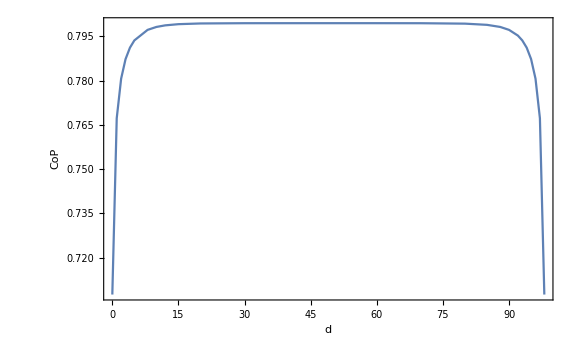

```mathematica
ListPlot[ListSubCaseExtra2,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

In this case, Complexity of Purification (CoP) seems to be monotonically increasing with the distance between the subsystems. There is no plateau-like structure for small separation. It can also be seen that for a separation of order 10^1, CoP saturates.

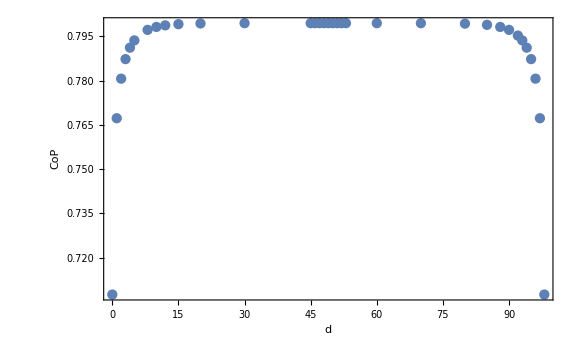
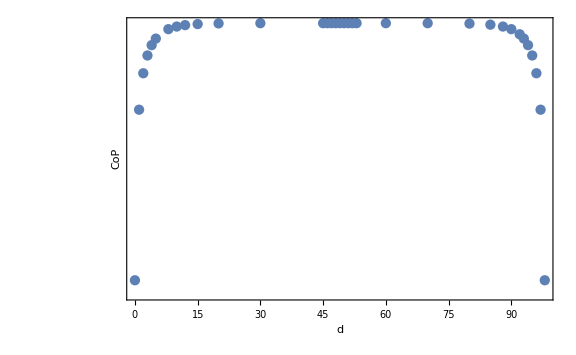

```mathematica
PlotListSubCaseExtra2=Row[{ListPlot[ListSubCaseExtra2,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50],ListLogPlot[ListSubCaseExtra2,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]}]
Export[NotebookDirectory[]<>"PlotListSubCaseExtra2.pdf",PlotListSubCaseExtra2];
```

```mathematica
Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,1]]
```

{0.055985,0.072577,0.067841,0.068742,0.069764,0.05509,0.059346,0.058956,0.05997,0.058424,0.059124,0.060084,0.062249,0.061462,0.072243,0.063182,0.071024}

```mathematica
(*Time=Table[Timing[GOOptimize[{function[[i]],gradient[[i]]},{JR0,M0List[[i]],LieBasis,IdentityMatrix[Length[LieBasis]],newM},ProcedureSpecific]][[All,1]],{i,Length[seplist]}]*)
```

```mathematica
(*Result=Table[Timing[GOOptimize[{function[[i]],gradient[[i]]},{JR0,M0List[[i]],LieBasis,IdentityMatrix[Length[LieBasis]],newM},ProcedureSpecific]][[All,2]],{i,Length[seplist]}];*)
```

```mathematica
(*Print["Time taken: ",Time," seconds"];
Print["Final value: ",Table[(Result[[i]])⟦1,1⟧,{i,Length[seplist]}]];
Print["Number of iterations: ",Length[Result⟦4,1⟧]];
Print["Number of total corrections: ",Result⟦3⟧//Total];
ListPlot[Result⟦4⟧, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]*)
(* We plot all items in the finalElist object in the result to ensure a correct plot in the case of multiple results *)
```

### SubCase 1.4: N=100, m=1/10, δ=1, dimA1=dimB1=8

IMPORTANT (04.09.19 - 13:21): SubCase 1.4 is being studied with the most recent function definitions (as of 30.08.19). In this subcase, we also use Schur Decomposition to find the correct transformation MTra that brings the mixed state covariance matrix to the standard form. 

UPDATE: (05.09.19 - 11:51): In SubCase 1.4.5, it seemed as if the Schur decomposition would no longer be needed. However, the transformation arising from the usual package implementation does not work. So, we continue using Schur decomposition.

```mathematica
sites=100;
mass=1/10;
latticespacing=1;
dimA1=8;
dimB1=8;
dimPur=dimA1+dimB1;
Arrayseplist={{0},{1},{2},{3},{4},{5},{8},{10},{12},{15},{20},{30},{40},{41},{42}};
seplist=Flatten[Arrayseplist];
```

```mathematica
TableCM0=Table[partialCM[sites,mass,latticespacing,seplist[[i]],dimA1,dimB1],{i,1,Length[seplist]}];
```

Here, the usual method of extracting the transformation doesn’t work. We need to use a Schur decomposition:

```mathematica
Table[Table[GOExtractStdFormG[TableCM0[[i]]],{i,1,Length[TableCM0]}][[j]],{j,1,Length[seplist]}][[All,2]]
```

Dot::dotsh: Tensors … and {«1»} have incompatible shapes.

Dot::dotsh: Tensors … and {{-0.000104995,-0.00119763,0.00694994,0.0283294,-0.0793539,-0.211306,0.348963,0.735672,-0.729043,-1.36234,0.746451,1.37107,-0.325009,«6»,-0.0284842,0.0236188,0.0390319,-0.00647977,-0.0157864,-0.00378468,-0.00399568,0.00113327,0.00296645,0.0000850978,-0.000102886,-9.65087×10^-6,-0.0000516727},«30»,{«21»,«30»,«23»}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

```mathematica
(*rlist=Table[Table[GOExtractStdFormG[TableCM0[[i]]],{i,1,Length[TableCM0]}][[j]],{j,1,Length[seplist]}][[All,1]];*)
(*MTra=Table[Table[GOExtractStdFormG[TableCM0[[i]]],{i,1,Length[TableCM0]}][[j]],{j,1,Length[seplist]}][[All,2]];*)
```

```mathematica
TableSqCM0=Table[MatrixPower[TableCM0⟦i⟧,-1/2],{i,1,Length[seplist]}]//Chop;
```

```mathematica
TableMat=Table[TableSqCM0⟦i⟧.GOΩqpqp[dimPur].TableSqCM0⟦i⟧,{i,1,Length[seplist]}]//Chop;
```

```mathematica
TableJJ=Table[(GOΩqpqp[dimPur].TableCM0⟦i⟧),{i,1,Length[seplist]}]//Chop;
```

```mathematica
qlist=Table[(SchurDecomposition[TableMat⟦i⟧]//Chop),{i,1,Length[seplist]}][[All,1]]//Chop;
```

```mathematica
tlist=Table[(SchurDecomposition[TableMat⟦i⟧]//Chop),{i,1,Length[seplist]}][[All,2]]//Chop;
```

```mathematica
(*sqCM0=MatrixPower[CM0,-1/2];
mat=sqCM0.GOΩqpqp[16].sqCM0;
N2=Length[CM0];
JJ=GOΩqpqp[N2/2].CM0;
{q,t}=SchurDecomposition[mat]//Chop;*)
```

```mathematica
MTra=Table[Transpose[TableSqCM0⟦i⟧.qlist⟦i⟧.MatrixPower[tlist⟦i⟧,-1/2]],{i,1,Length[seplist]}]//Chop;
```

```mathematica
rlist=Table[(1/2 ArcCosh[Select[Im[Eigenvalues[TableJJ⟦i⟧]]//Chop,#>0&]]//Chop),{i,1,Length[seplist]}]//Chop;
```

```mathematica
(*MTra=Transpose[sqCM0.q.MatrixPower[t,-1/2]];
rlist=1/2 ArcCosh[Select[Im[Eigenvalues[JJ]]//Chop,#>0&]]//Chop
MTra.CM0.Transpose[MTra]//Chop//MatrixForm*)
```

```mathematica
JT=Table[GOPurifyStandardJBoson[rlist[[i]],dimPur,"qpqp"]//Chop,{i,Length[seplist]}]//Chop;
JR0=GOTransformGtoJ[IdentityMatrix[2(dimA1+dimB1+dimPur)]//Chop,"qpqp","qpqp"]//Chop;
```

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra[[i]]],0},{0,IdentityMatrix[2dimPur]}}]//SparseArray,{i,Length[seplist]}];
```

```mathematica
function=Table[GOCoPBos[JT[[i]]],{i,Length[seplist]}]; 
gradient=Table[GOCoPgradBos[JT[[i]]],{i,Length[seplist]}];
```

```mathematica
ProblemSpecific=Table[{function[[i]],gradient[[i]]},{i,Length[seplist]}];
```

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSpNoUN[dimPur]}];
metric=GOMetricSp[LieBasis,JR0];
newM[m_,s_,x_]:=GOapproxExp[s,x].m;
```

```mathematica
SystemSpecific=Table[{JR0,{M0List[[i]]},LieBasis,IdentityMatrix[Length[LieBasis]],newM},{i,Length[M0List]}];
```

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-10; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

```mathematica
(*{Time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];*)
```

```mathematica
Timing[GOOptimize[ProblemSpecific[[1]],SystemSpecific[[1]],ProcedureSpecific]]
```

{1.56971}

Reason for termination: Function value tolerance reached

{40.782,{{1.56955},{SparseArray[…]},{3,3,3,3},{{1.56971,1.56955,1.56955,1.56955,1.56955}},{{1.56971,1.56955,1.56955,1.56955,1.56955}},{{0.367943,0.0258753,0.00183177,0.000129878,9.21728×10^-6}}}}

```mathematica
Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,2]][[All,1]]
```

{1.56971}

Reason for termination: Function value tolerance reached

{1.60774}

Reason for termination: Function value tolerance reached

{1.62076}

Reason for termination: Function value tolerance reached

{1.62813}

Reason for termination: Function value tolerance reached

{1.63283}

Reason for termination: Function value tolerance reached

{1.63601}

Reason for termination: Function value tolerance reached

{1.641}

Reason for termination: Function value tolerance reached

{1.64251}

Reason for termination: Function value tolerance reached

{1.64338}

Reason for termination: Function value tolerance reached

{1.64407}

Reason for termination: Function value tolerance reached

{1.64451}

Reason for termination: Function value tolerance reached

{1.64471}

Reason for termination: Function value tolerance reached

{1.64473}

Reason for termination: Function value tolerance reached

{1.64473}

Reason for termination: Function value tolerance reached

{1.64473}

Reason for termination: Function value tolerance reached

{{1.56955},{1.60737},{1.62036},{1.62771},{1.6324},{1.63556},{1.64053},{1.64204},{1.6429},{1.64358},{1.64402},{1.64421},{1.64424},{1.64424},{1.64424}}

```mathematica
ListSubCase14=Join[Arrayseplist,Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,2]][[All,1]],2];
```

{1.56971}

Reason for termination: Function value tolerance reached

{1.60774}

Reason for termination: Function value tolerance reached

{1.62076}

Reason for termination: Function value tolerance reached

{1.62813}

Reason for termination: Function value tolerance reached

{1.63283}

Reason for termination: Function value tolerance reached

{1.63601}

Reason for termination: Function value tolerance reached

{1.641}

Reason for termination: Function value tolerance reached

{1.64251}

Reason for termination: Function value tolerance reached

{1.64338}

Reason for termination: Function value tolerance reached

{1.64407}

Reason for termination: Function value tolerance reached

{1.64451}

Reason for termination: Function value tolerance reached

{1.64471}

Reason for termination: Function value tolerance reached

{1.64473}

Reason for termination: Function value tolerance reached

{1.64473}

Reason for termination: Function value tolerance reached

{1.64473}

Reason for termination: Function value tolerance reached

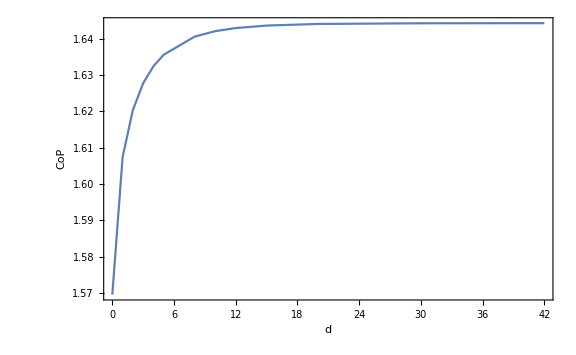

```mathematica
ListPlot[ListSubCase14,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

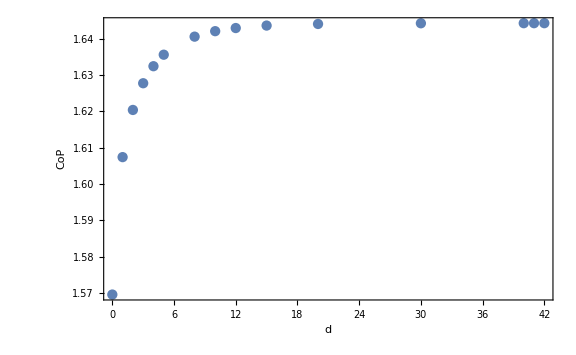
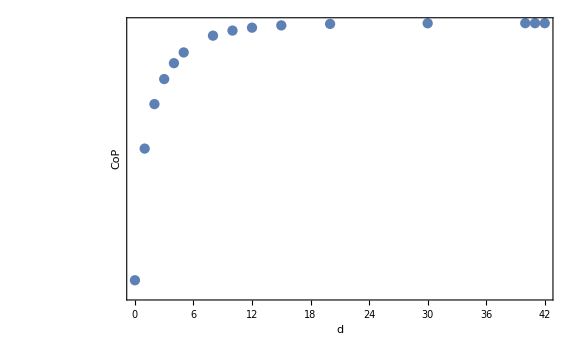

```mathematica
PlotListSubCase14=Row[{ListPlot[ListSubCase14,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50],ListLogPlot[ListSubCase14,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]}]
Export[NotebookDirectory[]<>"PlotListSubCase14.pdf",PlotListSubCase14];
```

```mathematica
Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,1]]
```

{1.56971}

Reason for termination: Function value tolerance reached

{1.60774}

Reason for termination: Function value tolerance reached

{1.62076}

Reason for termination: Function value tolerance reached

{1.62813}

Reason for termination: Function value tolerance reached

{1.63283}

Reason for termination: Function value tolerance reached

{1.63601}

Reason for termination: Function value tolerance reached

{1.641}

Reason for termination: Function value tolerance reached

{1.64251}

Reason for termination: Function value tolerance reached

{1.64338}

Reason for termination: Function value tolerance reached

{1.64407}

Reason for termination: Function value tolerance reached

{1.64451}

Reason for termination: Function value tolerance reached

{1.64471}

Reason for termination: Function value tolerance reached

{1.64473}

Reason for termination: Function value tolerance reached

{1.64473}

Reason for termination: Function value tolerance reached

{1.64473}

Reason for termination: Function value tolerance reached

{118.525,114.871,144.659,63.4983,63.7218,62.9841,49.1278,48.7656,49.2767,49.5509,49.8122,49.3996,46.8817,44.8484,42.4772}

### SubCase 1.5: N=100, m=1/10, δ=1, dimA1=dimB1=10

```mathematica
sites=100;
mass=1/10;
latticespacing=1;
dimA1=10;
dimB1=10;
dimPur=dimA1+dimB1;
Arrayseplist={{0},{1},{2},{3},{4},{5},{8},{10},{12},{15},{20},{30},{35},{38},{40}};
seplist=Flatten[Arrayseplist];
```

```mathematica
TableCM0=Table[partialCM[sites,mass,latticespacing,seplist[[i]],dimA1,dimB1],{i,1,Length[seplist]}];
```

Here, the usual method of extracting the transformation doesn’t work. We need to use a Schur decomposition:

```mathematica
Table[Table[GOExtractStdFormG[TableCM0[[i]]],{i,1,Length[TableCM0]}][[j]],{j,1,Length[seplist]}][[All,2]]
```

Dot::dotsh: Tensors … and {«1»} have incompatible shapes.

Dot::dotsh: Tensors … and {{-0.000104995,-0.00119763,0.00694994,0.0283294,-0.0793539,-0.211306,0.348963,0.735672,-0.729043,-1.36234,0.746451,1.37107,-0.325009,«6»,-0.0284842,0.0236188,0.0390319,-0.00647977,-0.0157864,-0.00378468,-0.00399568,0.00113327,0.00296645,0.0000850978,-0.000102886,-9.65087×10^-6,-0.0000516727},«30»,{«21»,«30»,«23»}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

```mathematica
(*rlist=Table[Table[GOExtractStdFormG[TableCM0[[i]]],{i,1,Length[TableCM0]}][[j]],{j,1,Length[seplist]}][[All,1]];*)
(*MTra=Table[Table[GOExtractStdFormG[TableCM0[[i]]],{i,1,Length[TableCM0]}][[j]],{j,1,Length[seplist]}][[All,2]];*)
```

```mathematica
TableSqCM0=Table[MatrixPower[TableCM0⟦i⟧,-1/2],{i,1,Length[seplist]}]//Chop;
```

```mathematica
TableMat=Table[TableSqCM0⟦i⟧.GOΩqpqp[dimPur].TableSqCM0⟦i⟧,{i,1,Length[seplist]}]//Chop;
```

```mathematica
TableJJ=Table[(GOΩqpqp[dimPur].TableCM0⟦i⟧),{i,1,Length[seplist]}]//Chop;
```

```mathematica
qlist=Table[(SchurDecomposition[TableMat⟦i⟧]//Chop),{i,1,Length[seplist]}][[All,1]]//Chop;
```

```mathematica
tlist=Table[(SchurDecomposition[TableMat⟦i⟧]//Chop),{i,1,Length[seplist]}][[All,2]]//Chop;
```

```mathematica
(*sqCM0=MatrixPower[CM0,-1/2];
mat=sqCM0.GOΩqpqp[16].sqCM0;
N2=Length[CM0];
JJ=GOΩqpqp[N2/2].CM0;
{q,t}=SchurDecomposition[mat]//Chop;*)
```

```mathematica
MTra=Table[Transpose[TableSqCM0⟦i⟧.qlist⟦i⟧.MatrixPower[tlist⟦i⟧,-1/2]],{i,1,Length[seplist]}]//Chop;
```

```mathematica
rlist=Table[(1/2 ArcCosh[Select[Im[Eigenvalues[TableJJ⟦i⟧]]//Chop,#>0&]]//Chop),{i,1,Length[seplist]}]//Chop;
```

```mathematica
(*MTra=Transpose[sqCM0.q.MatrixPower[t,-1/2]];
rlist=1/2 ArcCosh[Select[Im[Eigenvalues[JJ]]//Chop,#>0&]]//Chop
MTra.CM0.Transpose[MTra]//Chop//MatrixForm*)
```

```mathematica
JT=Table[GOPurifyStandardJBoson[rlist[[i]],dimPur,"qpqp"]//Chop,{i,Length[seplist]}]//Chop;
JR0=GOTransformGtoJ[IdentityMatrix[2(dimA1+dimB1+dimPur)]//Chop,"qpqp","qpqp"]//Chop;
```

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra[[i]]],0},{0,IdentityMatrix[2dimPur]}}]//SparseArray,{i,Length[seplist]}];
```

```mathematica
function=Table[GOCoPBos[JT[[i]]],{i,Length[seplist]}]; 
gradient=Table[GOCoPgradBos[JT[[i]]],{i,Length[seplist]}];
```

```mathematica
ProblemSpecific=Table[{function[[i]],gradient[[i]]},{i,Length[seplist]}];
```

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSpNoUN[dimPur]}];
metric=GOMetricSp[LieBasis,JR0];
newM[m_,s_,x_]:=GOapproxExp[s,x].m;
```

```mathematica
SystemSpecific=Table[{JR0,{M0List[[i]]},LieBasis,IdentityMatrix[Length[LieBasis]],newM},{i,Length[M0List]}];
```

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-10; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

```mathematica
(*{Time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];*)
```

```mathematica
Timing[GOOptimize[ProblemSpecific[[1]],SystemSpecific[[1]],ProcedureSpecific]]
```

{1.56971}

Reason for termination: Function value tolerance reached

{40.782,{{1.56955},{SparseArray[…]},{3,3,3,3},{{1.56971,1.56955,1.56955,1.56955,1.56955}},{{1.56971,1.56955,1.56955,1.56955,1.56955}},{{0.367943,0.0258753,0.00183177,0.000129878,9.21728×10^-6}}}}

```mathematica
Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,2]][[All,1]]
```

{{1.56955},{1.60737},{1.62036},{1.62771},{1.6324},{1.63556},{1.64053},{1.64204},{1.6429},{1.64358},{1.64402},{1.64421},{1.64424},{1.64424},{1.64424}}

```mathematica
ListSubCase14=Join[Arrayseplist,Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,2]][[All,1]],2];
```

```mathematica
ListPlot[ListSubCase14,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

-Graphics-

```mathematica
PlotListSubCase14=Row[{ListPlot[ListSubCase14,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50],ListLogPlot[ListSubCase14,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]}]
Export[NotebookDirectory[]<>"PlotListSubCase14.pdf",PlotListSubCase14];
```

-Graphics--Graphics-

```mathematica
Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,1]]
```

{118.525,114.871,144.659,63.4983,63.7218,62.9841,49.1278,48.7656,49.2767,49.5509,49.8122,49.3996,46.8817,44.8484,42.4772}

### SubCase 1.6: N=100, m=1/10, δ=1, dimS=20

### SubCase 1.7: N=100, m=1/10, δ=1, dimS=40

### SubCase 1.8: N=100, m=1/10, δ=1, dimS=45

### Summary Results Case 1

```mathematica
ListSubCase11
ListSubCase12
ListSubCase13
ListSubCase14
```

{{0,0.707459},{1,0.767223},{2,0.780635},{3,0.787262},{4,0.79114},{5,0.793601},{8,0.797171},{10,0.798164},{12,0.798703},{15,0.799105},{20,0.799346},{30,0.799434},{45,0.799442},{46,0.799442},{47,0.799442},{48,0.799443},{49,0.799443}}

{{0,0.890738},{1,0.956594},{2,0.973802},{3,0.982673},{4,0.987995},{5,0.991432},{8,0.996523},{10,0.99797},{15,0.999362},{20,0.999723},{30,0.999857},{40,0.999869},{43,0.99987},{47,0.99987},{48,0.99987}}

{{0,1.0354},{1,1.09587},{2,1.11317},{3,1.12242},{4,1.12812},{5,1.13188},{8,1.13761},{10,1.13931},{12,1.14026},{15,1.14101},{20,1.1415},{30,1.14171},{40,1.14174},{45,1.14175},{47,1.14175}}

{{0,1.56955},{1,1.60737},{2,1.62036},{3,1.62771},{4,1.6324},{5,1.63556},{8,1.64053},{10,1.64204},{12,1.6429},{15,1.64358},{20,1.64402},{30,1.64421},{40,1.64424},{41,1.64424},{42,1.64424}}

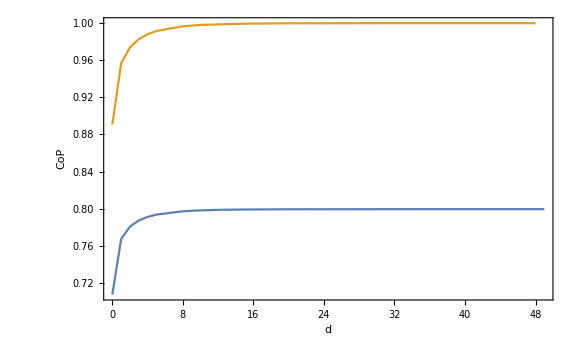

```mathematica
ListPlot[{ListSubCase11,ListSubCase12},PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

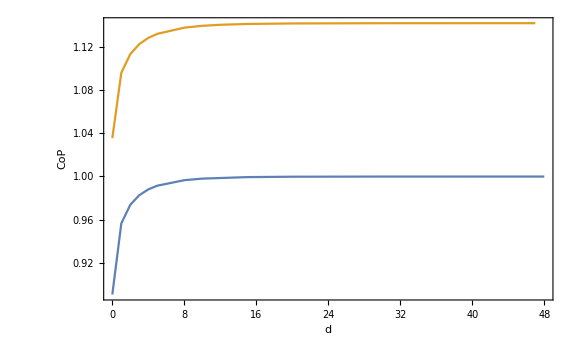

```mathematica
ListPlot[{ListSubCase12,ListSubCase13},PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

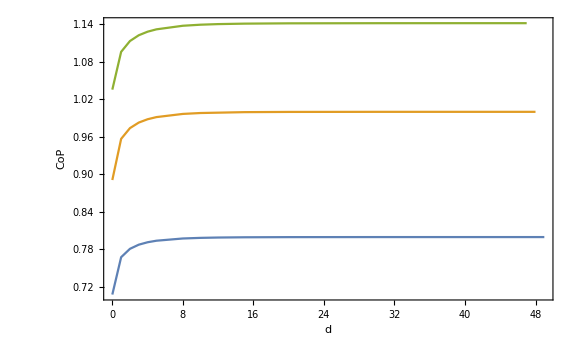

```mathematica
ListPlot[{ListSubCase11,ListSubCase12,ListSubCase13},PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

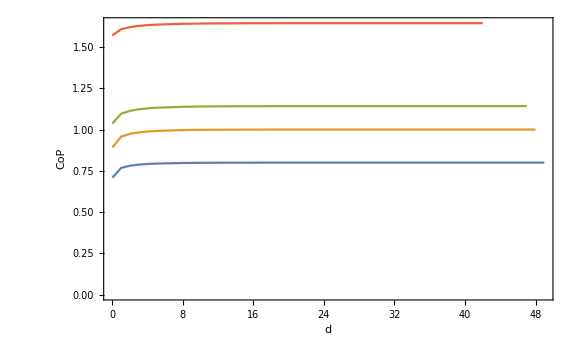

```mathematica
ListPlot[{ListSubCase11,ListSubCase12,ListSubCase13,ListSubCase14},PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

## Case 2: N=100, m=1/10, δ=1/10 ; (N-1)δ == L=9.9

### SubCase 2.1: N=100, m=1/10, δ=1/10, dimS=1

### SubCase 2.2: N=100, m=1/10, δ=1/10, dimS=2

### SubCase 2.3: N=100, m=1/10, δ=1/10, dimS=3

### SubCase 2.4: N=100, m=1/10, δ=1/10, dimS=5

### SubCase 2.5: N=100, m=1/10, δ=1/10, dimS=8

### SubCase 2.6: N=100, m=1/10, δ=1/10, dimS=10

### SubCase 2.7: N=100, m=1/10, δ=1/10, dimS=15

### SubCase 2.8: N=100, m=1/10, δ=1/10, dimS=20

### SubCase 2.9: N=100, m=1/10, δ=1/10, dimS=25

### SubCase 2.10: N=100, m=1/10, δ=1/10, dimS=40

### Summary Case 2

## Case 3: N=10, m=1/10, δ=1; (N-1)δ == L=9

### SubCase 3.1: N=10, m=1/10, δ=1, dimS=1

### SubCase 3.2: N=10, m=1/10, δ=1, dimS=2

### SubCase 3.3: N=10, m=1/10, δ=1, dimS=3

### SubCase 3.4: N=10, m=1/10, δ=1, dimS=4

### Summary Case 3

## Case 4: N=10, m=1/10, δ=1/10

### SubCase 4.1: N=10, m=1/10, δ=1/10, dimS=1

### SubCase 4.2: N=10, m=1/10, δ=1/10, dimS=2

### SubCase 4.3: N=10, m=1/10, δ=1/10, dimS=3

### SubCase 4.4: N=10, m=1/10, δ=1/10, dimS=4

### Summary Case 4

## Case 5: N=300, m=1/10, δ=1

### SubCase 5.1: N=300, m=1/10, δ=1, dimS=1

### SubCase 5.2: N=300, m=1/10, δ=1, dimS=2

### SubCase 5.3: N=300, m=1/10, δ=1, dimS=3

### SubCase 5.4: N=300, m=1/10, δ=1, dimS=5

### SubCase 5.5: N=300, m=1/10, δ=1, dimS=10

### SubCase 5.6: N=300, m=1/10, δ=1, dimS=15

### SubCase 5.7: N=300, m=1/10, δ=1, dimS=30

### SubCase 5.8: N=300, m=1/10, δ=1, dimS=50

### SubCase 5.9: N=300, m=1/10, δ=1, dimS=80

### SubCase 5.10: N=300, m=1/10, δ=1, dimS=100

### Summary Case 5

## Summary of Results Scenario 1

Scenario 2: BCoP as a Function of Subsystem Size (0 Separation)

## Case 1: N=100, m=1/10, δ=1

## Case 2: N=100, m=1/10, δ=1/10

## Case 3: N=10, m=1/10, δ=1

## Case 4: N=10, m=1/10, δ=1/10

## Case 5: N=300, m=1/10, δ=1

## Summary of Results Scenario 2

Scenario 3: CoP as a Function of Subsystem Size (Variable Separation)

## Case 1: N=100, m=1/10, δ=1

## Case 2: N=100, m=1/10, δ=1/10

## Case 3: N=100, m=1/10, δ=1

## Case 4: N=10, m=1/10, δ=1/10

## Case 5: N=300, m=1/10, δ=1

## Summary of Results Scenario 3

Scenario 4: CoP in the Continuum Limit?

## Case 1: N=300, m=1/10, δ=1/10

## Case 2: N=500, m=1/10, δ=1/10

## Case 3: N=800, m=1/10, δ=1/10

## Summary of Results Scenario 4

## Chapter 2: Bosons under a Smooth Quench Through a Critical Point

Definitions

```mathematica
(* note that w0 and ω0 are the same thing *)
```

```mathematica
(*Pawel and company work with something called ΓQ := ω0 dt. They also define something called tKZ = ξKZ = Sqrt[dt/ω0]=Sqrt[ΓQ/ω0^2], Kibble-Zurek time*)
```

```mathematica
(*Kibble-Zurek scaling for ΓQ>>1. Fast-quench-regime ΓQ<<1 but dt>1.*)
```

```mathematica
(*Initial Correlation Length ξI proportional to 1/ω0*)
```

```mathematica
(*repCorr={ω0->1/ξi};*)(*How to insert the lenght of the system?It's already there in L!*)
```

```mathematica
Solve[{ΓQ==ω0 dt&&ξI==1/ω0},{dt,ω0}]
```

{{dt→ΓQ ξI,ω0→1/ξI}}

```mathematica
repCorr={dt->ΓQ ξI,ω0->1/ξI};
```

```mathematica
Solve[{ΓQ==ω0 dt && ξKZ^2==dt/ω0},{dt,ω0}]
```

{{dt→-√ΓQ ξKZ,ω0→-(√ΓQ)/ξKZ},{dt→√ΓQ ξKZ,ω0→(√ΓQ)/ξKZ}}

```mathematica
repPar={dt->√ΓQ ξKZ,ω0->(√ΓQ)/ξKZ};
```

```mathematica
$Assumptions=And[$Assumptions&& ΓQ ∈ Reals&&ξKZ ∈ Reals && ΓQ > 0 && ξKZ > 0];
```

```mathematica
$Assumptions=And[$Assumptions&&ξI∈Reals&&ξI>0];
```

Definitions from the exact solution with ω_0 as a parameter (taken from Diptarka’s file and checked with Pawel’s paper) :

```mathematica
ω[k_,ω0_]:= Sqrt[ 4 Sin[k/2]^2 + ω0^2];
α[dt_,ω0_]:= 1/4(1 + Sqrt[1- 4 ω0^2 dt^2]);
a[k_,dt_,ω0_]:= α[dt,ω0] + I/2 dt ω[k,ω0];
b[k_,dt_,ω0_]:= α[dt,ω0] - I/2 dt ω[k,ω0];
e12[k_,dt_,ω0_]:= (Gamma[1/2]Gamma[b[k,dt,ω0]-a[k,dt,ω0]])/(Gamma[b[k,dt,ω0]]Gamma[1/2-a[k,dt,ω0]]);
e12p[k_,dt_,ω0_]:= (Gamma[1/2]Gamma[a[k,dt,ω0]-b[k,dt,ω0]])/(Gamma[a[k,dt,ω0]]Gamma[1/2-b[k,dt,ω0]]);
e32[k_,dt_,ω0_]:= (Gamma[3/2]Gamma[b[k,dt,ω0]-a[k,dt,ω0]])/(Gamma[1/2+b[k,dt,ω0]]Gamma[1-a[k,dt,ω0]]);
e32p[k_,dt_,ω0_]:= (Gamma[3/2]Gamma[a[k,dt,ω0]-b[k,dt,ω0]])/(Gamma[1/2+a[k,dt,ω0]]Gamma[1-b[k,dt,ω0]]);
f[k_,dt_,x_,ω0_]:= 1/Sqrt[2 ω[k,ω0]] (((2)^(I ω[k,ω0]dt)Cosh[x]^(2 α[dt,ω0]))/(e12p[k,dt,ω0]e32[k,dt,ω0]-e12[k,dt,ω0]e32p[k,dt,ω0]))(e32p[k,dt,ω0] Hypergeometric2F1[a[k,dt,ω0],b[k,dt,ω0],1/2, -Sinh[x]^2] + e12p[k,dt,ω0] Sinh[x] Hypergeometric2F1[a[k,dt,ω0]+1/2, b[k,dt,ω0]+1/2, 3/2, -Sinh[x]^2]);
(*Df[k_,dt_,x_,ω0_]:=( 1/dt( D[f[k,dt,y,ω0],y])/.y->x);*)
Module[{exp=( 1/dt( D[f[k,dt,y,ω0],y])/.y->x)},Df[kval_,dtval_,xval_,ω0val_]:=exp//.{k-> kval,dt-> dtval,x-> xval,ω0-> ω0val};]
ff[k_,dt_,x_,ω0_]:=  I Conjugate[ Df[k,dt,x,ω0]/f[k,dt,x,ω0]]/ω[k,ω0];
ff1[k_,dt_,x_,ω0_]:=  I Conjugate[ Df[k,dt,x,ω0]/f[k,dt,x,ω0]]/ω0;
```

## Static Adiabatic Wavefunction

```mathematica
fadiak[k_,dt_,x_,ω0_]:=1/Sqrt[2 √(4 Sin[k/2]^2+ω0^2 Tanh[x]^2)] Exp[-I √(4 Sin[k/2]^2+ω0^2 Tanh[x]^2) (dt x )];
```

```mathematica
ωadiak[k_,x_,ω0_]:= √(4 Sin[k/2]^2+ω0^2 Tanh[x]^2);
```

```mathematica
(*Dfadiak[k_,dt_,x_,ω0_]:=( 1/dt( D[fadiak[k,dt,y,ω0],y])/.y->x);*)
```

```mathematica
Module[{exp=( 1/dt( D[fadiak[k,dt,y,ω0],y])/.y->x)},Dfadiak[kval_,dtval_,xval_,ω0val_]:=exp//.{k-> kval,dt-> dtval,x-> xval,ω0-> ω0val};]
ffadiak[k_,dt_,x_,ω0_]:=  I Conjugate[ Dfadiak[k,dt,x,ω0]/fadiak[k,dt,x,ω0]]/ωadiak[k,x,ω0];
ff1adiak[k_,dt_,x_,ω0_]:=  I Conjugate[ Dfadiak[k,dt,x,ω0]/fadiak[k,dt,x,ω0]]/ω0;
```

## Correlators

```mathematica
(*Expressions taken from https://arxiv.org/pdf/1702.04359.pdf Eqs. 13*)
```

```mathematica
(*dt->ΓQ ξI,ω0->1/ξI*)
```

```mathematica
Xmn[dt_,x_,ω0_,m_,n_]:=1/(2 π)NIntegrate[Abs[f[k,dt,x,ω0]]^2 Cos[k Abs[m-n]],{k,-π, π},WorkingPrecision->30,MaxRecursion->30];
```

```mathematica
Pmn[dt_,x_,ω0_,m_,n_]:=1/(2 π)NIntegrate[Abs[Df[k,dt,x,ω0]]^2 Cos[k Abs[m-n]],{k,-π, π},WorkingPrecision->30,MaxRecursion->30];
```

```mathematica
Dmn[dt_,x_,ω0_,m_,n_]:=1/(2 π)NIntegrate[Re[Conjugate[f[k,dt,x,ω0]]Df[k,dt,x,ω0]]Cos[k Abs[m-n]],{k,-π, π},WorkingPrecision->30,MaxRecursion->30];
```

```mathematica
{Xmn[1,0,1,1,1],Pmn[1,0,1,1,1],Dmn[1,0,1,1,1]}
```

{0.458879124592772692390794947403,0.680419473195872175101848907276,0.0893033409694448901693926712853}

```mathematica
repPar
```

{dt→√ΓQ ξKZ,ω0→(√ΓQ)/ξKZ}

```mathematica
repCorr
```

{dt→ΓQ ξI,ω0→1/ξI}

```mathematica
$Assumptions=And[$Assumptions&&m ∈Integers&&n∈Integers];
```

```mathematica
XmnΓ[ΓQ_,x_,ξI_,m_,n_]:=1/(2 π)Quiet@NIntegrate[Abs[f[k,ΓQ ξI,x,1/ξI]]^2 Cos[k Abs[m-n]],{k,-π, π},WorkingPrecision->30,MaxRecursion->30];
```

```mathematica
PmnΓ[ΓQ_,x_,ξI_,m_,n_]:=1/(2 π)Quiet@NIntegrate[Abs[Df[k,ΓQ ξI,x,1/ξI]]^2 Cos[k Abs[m-n]],{k,-π, π},WorkingPrecision->30,MaxRecursion->30];
```

```mathematica
DmnΓ[ΓQ_,x_,ξI_,m_,n_]:=1/(2 π)Quiet@NIntegrate[Re[Conjugate[f[k,ΓQ ξI,x,1/ξI]]Df[k,ΓQ ξI,x,1/ξI]]Cos[k Abs[m-n]],{k,-π, π},WorkingPrecision->30,MaxRecursion->30];
```

```mathematica
{XmnΓ[1,0,1,1,1],PmnΓ[1,0,1,1,1],DmnΓ[1,0,1,1,1]}
```

{0.458879124592772692390794947403,0.680419473195872175101848907276,0.0893033409694448901693926712853}

```mathematica
(*Call Mn:=Abs[m-n]*)
```

```mathematica
$Assumptions=And[$Assumptions&& Mn∈Reals&&Mn≥ 0];
```

```mathematica
(*$MaxExtraPrecision=mp*)
```

```mathematica
(*Block[{$MaxExtraPrecision=mp},N[MQ[[Abs[ii-jj]+1]],mp]];*)
```

```mathematica
XMnΓ[ΓQ_,x_,ξI_,Mn_]:=1/(2 π)NIntegrate[Abs[f[k,ΓQ ξI,x,1/ξI]]^2 Cos[k Mn],{k,-π, π},WorkingPrecision->20,AccuracyGoal->20,MaxRecursion->100];
```

```mathematica
PMnΓ[ΓQ_,x_,ξI_,Mn_]:=1/(2 π)NIntegrate[Abs[Df[k,ΓQ ξI,x,1/ξI]]^2 Cos[k Mn],{k,-π, π},WorkingPrecision->20,AccuracyGoal->20,MaxRecursion->100];
```

```mathematica
DMnΓ[ΓQ_,x_,ξI_,Mn_]:=1/(2 π)NIntegrate[Re[Conjugate[f[k,ΓQ ξI,x,1/ξI]]Df[k,ΓQ ξI,x,1/ξI]]Cos[k Mn],{k,-π, π},WorkingPrecision->20,AccuracyGoal->20, MaxRecursion->100];
```

```mathematica
{XMnΓ[1,0,1,0],PMnΓ[1,0,1,0],DMnΓ[1,0,1,0]}
```

{0.45887912459277269239,0.68041947319587217641,0.089303340969444890177}

```mathematica
N[Precision[XMnΓ[1,0,1,0]]]
```

20.

```mathematica
(*A plot for the sake of it*)
```

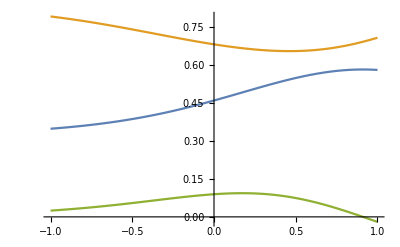

```mathematica
Plot[{XMnΓ[1,t,1,0],PMnΓ[1,t,1,0],DMnΓ[1,t,1,0]},{t,-1,1},PlotRange->All]
```

```mathematica
Jl[L_]:=KroneckerProduct[{{0,1},{-1,0}},IdentityMatrix[L]];
```

```mathematica
Jl[2]//MatrixForm
```

(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0)

```mathematica
Ω[tot_]:=SparseArray[{{x_,y_}/;x-y==-1&&OddQ[x]-> 1,{x_,y_}/;x-y==1&&OddQ[y]->-1},{2tot,2tot}]//Normal;
```

```mathematica
Ω[2]//MatrixForm
```

(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)

```mathematica
XmnΓtabRex[ΓQ_,x_,ξI_,L_]:=XmnΓtabRex[ΓQ,x,ξI,L]=Module[{XmntabC},
XmntabC=Table[XmnΓ[ΓQ,x,ξI,m,n],{m,1,L},{n,1,L}];XmntabC]
```

```mathematica
PmnΓtabRex[ΓQ_,x_,ξI_,L_]:=PmnΓtabRex[ΓQ,x,ξI,L]=Module[{PmntabC},
PmntabC=Table[PmnΓ[ΓQ,x,ξI,m,n],{m,1,L},{n,1,L}];PmntabC]
```

```mathematica
DmnΓtabRex[ΓQ_,x_,ξI_,L_]:=DmnΓtabRex[ΓQ,x,ξI,L]=Module[{DmntabC},
DmntabC=Table[DmnΓ[ΓQ,x,ξI,m,n],{m,1,L},{n,1,L}];DmntabC]
```

```mathematica
(*Nice!*)
```

```mathematica
(*CmnΓtabRex3 is the correct thing to use.*)
```

```mathematica
ToeXMnΓ[ΓQ_, x_, ξI_, L_]:=ToeXMnΓ[ΓQ,x,ξI,L]=ToeplitzMatrix[Table[XMnΓ[ΓQ,x,ξI,Mn],{Mn,0,L-1}]];
```

```mathematica
ToePMnΓ[ΓQ_, x_, ξI_, L_]:=ToePMnΓ[ΓQ,x,ξI,L]=ToeplitzMatrix[Table[PMnΓ[ΓQ,x,ξI,Mn],{Mn,0,L-1}]];
```

```mathematica
ToeDMnΓ[ΓQ_, x_, ξI_, L_]:=ToeDMnΓ[ΓQ,x,ξI,L]=ToeplitzMatrix[Table[DMnΓ[ΓQ,x,ξI,Mn],{Mn,0,L-1}]];
```

```mathematica
CmnΓtabRex3[ΓQ_,x_,ξI_,L_]:=ArrayFlatten[{{ToeXMnΓ[ΓQ,x,ξI,L],ToeDMnΓ[ΓQ,x,ξI,L]},{ToeDMnΓ[ΓQ,x,ξI,L],ToePMnΓ[ΓQ,x,ξI,L]}}];
```

CoP as a Function of Subsystem Separation (Fixed Subsystem Size)

CoP as a Function of Subsystem Size (0 Separation)

CoP as a Function of Subsystem Size (Variable Separation)

CoP in the Continuum Limit?